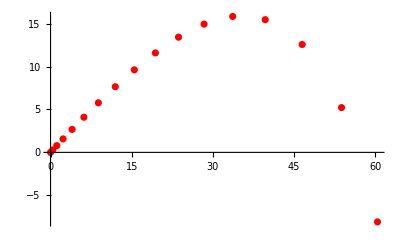

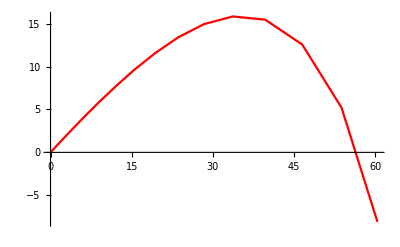

Approximate fall is:56.3556

```mathematica
(*Тъй като се решава векторно, правя промяна в стандартния RK45*)
(*Първо търся грешка-вектор между двете решения, а след това неговата норма*)
(*Тъй като се интерсуваме до къде ще падне ракетата, решаваме до дост. на y<=0*)
RK45Rocket[f_,t0_,h0_,tol_,y0_]:=(

a=List[0,1/4,3/8,12/13,1,1/2];

b={
{0,0,0,0,0,0},
{1/4,0,0,0,0,0},
{3/32,9/32,0,0,0,0},
{1932/2197,-7200/2197,7296/2197,0,0,0},
{439/216,-8,3680/513,-845/4104,0,0},
{-8/27,2,-3544/2565,1859/4104,-11/40,0}
};

p6=List[16/135,0,6656/12825,28561/56430,-9/50,2/55];
p5=List[25/216,0,1408/2565,2197/4104,-1/5,0];
p={p6,p5};

y=List[y0];
t=List[t0];
err=List[0];
tc=t0;
yc=y0;
hc=h0;

While[yc[[2]]>=0,
k=Table[{0,0,0,0},6];

For[s=1,s≤6,s++,
	k[[s]]=hc*f[tc+a[[s]]*hc,yc+Transpose[k].b[[s]]];
];

errcvec=Transpose[k].(p[[1]]-p[[2]]);
errc=Norm[errcvec]/Norm[yc];
hnext=hc*Power[tol/errc,1/5];

If[errc>tol,hc=hnext;Continue[],0];

yc=yc+Transpose[k].p[[1]];
AppendTo[y,yc];
tc=tc+hc;
AppendTo[t,tc];
AppendTo[err,errc];
hc=hnext;
];

res={t,y,err};
res
)

(*Условие*)
c=0.2;
g=9.81;
m=15;
rho=1.29;
s=0.25;

t0=0;
x0=0;
y0=0;
v0=50;
theta0=0.6;

f[t_,u_List]:={u[[3]]*Cos[u[[4]]],u[[3]]*Sin[u[[4]]],-(c*rho*s*u[[3]]^2)/(2*m)-g*Sin[u[[4]]],-g*Cos[u[[4]]]/u[[3]]};

u0={x0,y0,v0,theta0};
h0=0.01;
tol=10^(-2);

(*Решение*)
rcktTrj=RK45Rocket[f,t0,h0,tol,u0];
m=Length[rcktTrj[[1]]];
ListPlot[Table[{rcktTrj[[2]][[k]][[1]],rcktTrj[[2]][[k]][[2]]},{k,1,m}],PlotStyle->Red]
ListLinePlot[Table[{rcktTrj[[2]][[k]][[1]],rcktTrj[[2]][[k]][[2]]},{k,1,m}],PlotStyle->Red]

(*Приближена точка на падане*)
finalLine=Solve[rcktTrj[[2]][[m-1]][[1]]+ycoeff*rcktTrj[[2]][[m-1]][[2]]+stc==0&&
	rcktTrj[[2]][[m]][[1]]+ycoeff*rcktTrj[[2]][[m]][[2]]+stc==0,{ycoeff,stc}];
approxFall=-(stc/.finalLine)[[1]];
Style["Approximate fall is:"<>ToString[approxFall],FontSize->24]
```